# Learning XOR

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
numBooleanVariables=10; (* 2^numBooleanVariables possible inputs *)
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=Min[2000,2^numBooleanVariables];
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->bf@@x]&,Range[maxExamples]];
```

```mathematica
Take[examples,3]
```

{{0.,1.,1.,1.,0.,0.,0.,0.,1.,0.}→False,{0.,1.,0.,0.,0.,0.,1.,1.,0.,0.}→True,{1.,1.,0.,0.,0.,1.,1.,0.,0.,0.}→False}

```mathematica
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
targetEncoder=NetEncoder[{"Class",{True,False},"IndicatorVector"}];
```

## Create net

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNOT[inputSize,classificationLayerSize],
HardNeuralMajority[classificationLayerSize,inputSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralMajority[1,inputSize]
}];
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralNOT[inputSize,5]
}];
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralAND[inputSize,5]
}];
```

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralNOT[inputSize,5],
HardNeuralAND[inputSize,5]
}];
```

```mathematica
softNet
```

NetChain[<>]

```mathematica
(* N.B. 0.5 causes a hardening problem *)
input={0.1,0.2,0.3,0.4,0.51,0.6,0.7,0.8,0.9, 1.0};
```

```mathematica
Round[softNet[{input}]]
```

{0,1,1,1,1}

```mathematica
weights=ExtractWeights[softNet];
```

```mathematica
First[Boole[hardNet[{Harden[input],Harden[weights]}]]]
```

reshapedWeights  {{False,False,False,True,True,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False}}

notWeights  {{True,True,True,False,False,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True}}

Failure[…]

```mathematica
trainableSoftNet=NetGraph[<|"NeuralLogicNet"->softNet,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"},"Target"->targetEncoder];
```

```mathematica
NetFlatten[trainableSoftNet]
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableSoftNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,{},
"Output"->NetDecoder[targetEncoder]]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]
]};
```

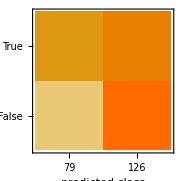
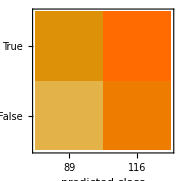
{Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (57.63.5) %
Accuracy baseline | (52.73.5) %
Geometric mean of probabilities | 0.5 ± 0.0038
Mean cross entropy | 0.693 ± 0.0075
Single evaluation time | 1.98 ms/example
Batch evaluation speed | 2.6 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (50.73.5) %
Accuracy baseline | (52.73.5) %
Geometric mean of probabilities | 0.439 ± 0.022
Mean cross entropy | 0.823 ± 0.05
Single evaluation time | 2.73 ms/example
Batch evaluation speed | 6.57 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder],First[#]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&/@testData;
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.560976

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

0.0390625 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Target",Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

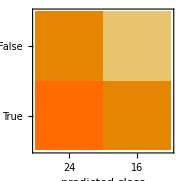
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 40
Accuracy | (55.8.) %
Accuracy baseline | (60.8.) %
Geometric mean of probabilities | 0.464 ± 0.038
Mean cross entropy | 0.768 ± 0.081
Single evaluation time | 4.81 ms/example
Batch evaluation speed | 518. examples/s
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Target"]
```

```mathematica
(First@classifier)["Model"]["Network"]
```

NetChain[<>]

```mathematica
Information[classifier,"FunctionMemory"]
```

290. kB

```mathematica
HNM[inputs_]:={Sort[inputs][[Floor[(Length[inputs]+1)/2]]],First[HardNeuralMajority[1,4]][{inputs}],Majority@@Harden[inputs]}
```

```mathematica
HNM[inputs_]:=With[{hnm=HardNeuralMajority[1,Length[inputs]]},{hnm[[1]][{inputs}],First[hnm[[2]][{{Harden[inputs]},{}}]]}]
```

```mathematica
Manipulate[HNM[{b1,b2,b3,b4}],{b1,0,1},{b2,0,1},{b3,0,1},{b4,0,1}]
```